```mathematica
data1=Drop[ResourceFunction["ImportCSVToDataset"]["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/DataAnalysis/GUISpectrumDatatest.csv"]None,3];
```

Drop::drop: Cannot drop positions 1 through 3 in None (Dataset[«1017»]).

Drop[None ,3]

```mathematica
satAbsTable= Transpose[Import["/Users/charlottezehnder/Documents/Academic/Summer 2021 Phys REU/laserStabilization/DataAnalysis/paramTraceTest.csv",{"Data",All,{2,4}}]]
```

{{RelativeTime (s),0.,1.006,2.001,3.,4.006,4.997,6.,7.008,7.998,9.006,10.007,10.997,12.,13.,13.995,15.001,15.997,17.005,18.008,19.001,20.007,20.997,22.001,23.,23.997,25.001,26.001,26.999,28.005,28.995,29.996,31.001,32.004,32.995,34.,35.005,35.999,37.002,37.997,39.003,40.,41.001,42.,43.001,44.009,44.996,46.,46.999,48.005,49.,50.003,51.003,52.001,53.,54.,54.996,56.009,56.997,58.006,58.995,59.996,61.002,61.998,63.001,63.996,65.006,65.996,67.006,67.999,69.002,70.007,71.008,72.012,73.013,74.019,75.013,76.016,77.011,78.017,79.017,80.015,81.017,82.019,83.011,84.013,85.014,86.019,87.012,88.018,89.016,90.02,91.011,92.014,93.025,94.015,95.025,96.022,97.022,98.025,99.021,100.011,101.016,102.017,103.016,104.021,105.012,106.017,107.017,108.015,109.021,110.017,111.016,112.019,113.022,114.011,115.017,116.011,117.017,118.015,119.022,120.016,121.011,122.015,123.017,124.012,125.017,126.019,127.02,128.025,129.023,130.014,131.017,132.039,133.028,134.031,135.033,136.029,137.03,138.038,139.032,140.04,141.035,142.027,143.047,144.054,145.063,146.065,147.068,148.058,149.058,150.064,151.065,152.065,153.062,154.06,155.065,156.06,157.065,158.065,159.065,160.069,161.071,162.063,163.069,164.06,165.063,166.065,167.058,168.062,169.065,170.063,171.068,172.065,173.062,174.065,175.07,176.071,177.06,178.06,179.06,180.061,181.064,182.06,183.063,184.063,185.066,186.061,187.066,188.071,189.077,190.08,191.079,192.085,193.075,194.073,195.086,196.078,197.085,198.08,199.089,200.1,201.09,202.093,203.101,204.089,205.096,206.103,207.094,208.111,209.106,210.112,211.106,212.107,213.11,214.105,215.105,216.106,217.11,218.105,219.106,220.11,221.105,222.115,223.11,224.108,225.114,226.118,227.112,228.105,229.109,230.105,231.109,232.11,233.105,234.105,235.112,236.113,237.106,238.111,239.116,240.112,241.117,242.107,243.11,244.118,245.111,246.107,247.115,248.107,249.115,250.118,251.107,252.105,253.106,254.105,255.114,256.11,257.119,258.105,259.107,260.11,261.11,262.11,263.105,264.11,265.111,266.111,267.105,268.115,269.109,270.11,271.109,272.117,273.11,274.107,275.11,276.115,277.112,278.115,279.11,280.111,281.106,282.115,283.106,284.105,285.116,286.105,287.106,288.105,289.115,290.11,291.11,292.105,293.11,294.115,295.106,296.114,297.106,298.11,299.11,300.111,301.108,302.115,303.11,304.111,305.115,306.117,307.113,308.119,309.105,310.115,311.108,312.118,313.105,314.115,315.109,316.11,317.109,318.105,319.105,320.111,321.115,322.112,323.11,324.113,325.115,326.105,327.106,328.116,329.109,330.115,331.118,332.105,333.114,334.116,335.11,336.115,337.112,338.109,339.105,340.115,341.12,342.122,343.344,344.126,345.123,346.121,347.122,348.12,349.121,350.12,351.131,352.122,353.132,354.124,355.13,356.124,357.134,358.128,359.12,360.121,361.13,362.13,363.124,364.125,365.13,366.13,367.13,368.134,369.12,370.12,371.279,372.12,373.122,374.126,375.129,376.12,377.125,378.122,379.12,380.122,381.129,382.131,383.137,384.143,385.145,386.14,387.141,388.145,389.139},{Fine 2 (V),0.000178,0.000504,0.000504,0.000152,0.000152,0.000152,0.000512,0.000526,0.000526,0.000505,0.000505,0.000505,0.000514,0.000514,0.000514,0.000514,0.000055,0.000055,0.000113,0.000113,8.×10^-6,8.×10^-6,0.000495,0.000495,0.000524,0.000524,0.000518,0.000518,0.000489,0.000489,0.000489,0.000508,0.000508,0.000527,0.000527,0.00052,0.00052,0.000493,0.000493,0.000509,0.000509,0.000509,0.000509,0.000435,0.000435,0.000293,0.000293,0.000532,0.000532,0.000203,0.000203,0.000521,0.000521,0.000511,0.000511,0.000511,0.000524,0.000524,0.000507,0.000507,-0.000514,-0.000514,0.000484,0.000484,0.000427,0.000427,0.000516,0.000516,0.000539,0.000539,0.000484,0.000484,0.000519,0.000519,0.000459,0.000459,0.000523,0.000523,-0.001154,-0.001154,0.000521,0.000521,0.000521,0.000502,0.000529,0.000529,0.000529,0.000235,0.000235,0.00052,0.00052,-0.001006,-0.001006,0.000484,0.000484,0.000506,0.000506,0.000528,0.000528,0.000491,0.000491,0.000533,0.000533,0.0005,0.0005,0.0005,0.000506,0.000506,0.000527,0.000527,0.000519,0.000519,0.000487,0.000487,0.0005,0.0005,-0.000723,-0.000723,0.000458,0.000458,0.000515,0.000515,0.000294,0.000294,0.000522,0.000522,0.000514,0.000514,0.000491,0.000491,0.000538,0.000538,0.000532,0.000532,0.000375,0.000375,0.000508,0.000508,0.000524,0.000524,0.000524,-0.002541,-0.002541,0.00026,0.00026,0.000518,0.000518,0.000557,0.000557,0.000533,0.000533,0.000527,0.000527,0.000369,0.000369,0.000473,0.000473,0.000473,0.000515,0.000515,0.000532,0.000532,0.000522,0.000522,-0.00083,-0.00083,0.000545,0.000545,0.000065,0.000065,0.000524,0.000524,0.000519,0.000519,0.000519,0.000472,0.000472,0.000524,0.000524,0.000518,0.000518,0.000386,0.000386,0.000532,0.000532,0.000454,0.000454,0.000521,0.000521,0.000507,0.000507,0.000532,0.000532,0.000535,0.000535,0.000522,0.000522,0.000529,0.000529,0.000503,0.000503,0.000503,0.000526,0.000526,0.000116,0.000116,0.000516,0.000516,0.00054,0.00054,0.000528,0.000528,0.000496,0.000496,0.000491,0.000491,0.000518,0.000518,0.00053,0.00053,0.00052,0.00052,0.000526,0.000526,0.000526,-0.003112,-0.003112,0.000459,0.000459,0.000517,0.000517,0.000482,0.000482,0.000516,0.000516,0.000424,0.000424,0.000424,0.000506,0.000506,-0.001177,-0.001177,-0.000148,-0.000148,0.000295,0.000295,-0.001325,-0.001325,0.000517,0.000517,0.000491,0.000491,0.000521,0.000521,0.000544,0.000544,-0.000479,-0.000479,0.000524,0.000524,0.000522,0.000522,0.000519,0.000519,0.000528,0.000528,0.000528,0.000225,0.000225,0.000368,0.000368,0.000499,0.000499,-0.001034,-0.001034,0.000038,0.000038,0.000234,0.000234,0.0002,0.0002,0.000522,0.000522,0.000528,0.000528,0.000509,0.000509,0.000524,0.000524,0.000504,0.000504,0.000505,0.000505,0.000505,0.000505,0.000414,0.000414,0.000519,0.000519,0.000536,0.000536,0.000498,0.000498,-0.006099,-0.006099,0.000514,0.000514,-0.000136,-0.000136,0.000447,0.000447,0.000508,0.000508,0.000521,0.000521,0.000521,0.000481,0.000481,-0.002597,-0.002597,0.000449,0.000449,-0.000716,-0.000716,-0.002104,-0.002104,0.000328,0.000328,0.000419,0.000419,0.000514,0.000514,0.000506,0.000506,0.000524,0.000524,0.000489,0.000489,0.000508,0.000508,0.000339,0.000339,0.00048,0.00048,0.000512,0.000512,-0.002874,-0.002874,-0.002874,0.000562,0.000562,0.000526,0.000526,0.000525,0.000525,0.000511,0.000511,-3.×10^-6,-3.×10^-6,0.00047,0.00047,0.000537,0.000537,0.000515,0.000515,0.000515,0.000529,0.000529,0.000519,0.000519,0.000536,0.000536,0.000521,0.000521,0.000513,0.000513,0.000512,0.000512,0.000442,0.000442,0.000442,0.000527,0.000527,0.000521,0.000521,0.000521,0.000521,-0.000376,-0.000376,0.000527}}

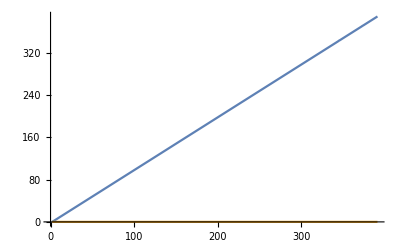

```mathematica
ListLinePlot[satAbsTable,PlotRange->Automatic]
```

```mathematica
Table[Accumulate[RandomReal[{-1,1},250]],{3}]
```

{{0.903941,1.24248,2.15019,2.5037,2.61251,3.00784,2.9347,2.76559,2.99881,2.71569,2.82947,2.3304,2.74317,2.33233,2.36634,1.48802,1.20313,1.11604,1.52438,0.69775,0.200317,-0.787259,-0.313437,-0.554346,-0.417489,-0.988604,-1.18879,-0.308372,-1.02684,-1.59127,-1.45338,-0.987764,-0.15786,0.179623,0.779947,1.62023,2.15809,3.03396,2.04571,2.63711,2.48184,3.47291,4.06169,4.7685,4.37813,4.64668,3.98625,3.22769,4.19185,3.43318,3.35275,3.63352,3.99553,4.33002,3.49151,4.47201,4.74698,5.03094,6.02395,6.93162,6.17559,6.61944,6.09373,5.56485,5.63762,6.05457,7.00422,6.2032,7.12452,7.37135,7.57319,7.58738,8.23907,7.64356,6.76519,6.02368,6.80641,7.65999,7.88702,8.30886,7.88146,6.91149,7.34917,6.36794,6.42432,6.92473,6.69615,6.63527,6.89494,6.98425,7.38305,7.72685,6.85476,7.6674,7.4831,7.40694,8.15995,8.69174,8.43564,8.31599,7.6312,6.69426,6.69088,6.64515,7.50906,6.6281,7.05287,8.02373,8.37972,8.56614,9.16965,8.68577,9.29398,9.81591,10.783,10.5571,9.9516,10.7463,11.3056,10.6283,10.1799,11.0064,11.4508,11.1646,10.2098,9.46234,9.99738,9.3171,8.83924,8.0263,7.95696,8.19996,8.36231,7.43389,7.73622,6.94292,7.83293,8.67471,8.4187,7.46534,6.68469,7.00418,7.81834,7.89391,8.19742,8.55066,8.89265,9.78632,8.88148,9.61917,10.4843,9.73328,9.66339,10.1004,9.59067,9.55589,9.88999,8.95259,9.21081,8.81729,9.08611,9.16299,8.79579,8.0041,7.66271,7.10844,6.53033,5.55491,6.48259,7.20211,6.20317,5.88598,5.29389,4.70021,5.43403,6.25961,5.36624,5.87342,4.88685,4.68032,5.39782,6.04173,5.06866,5.29664,5.05547,5.33419,6.00209,5.36404,4.59234,4.13825,3.90078,4.51034,4.1673,3.90838,4.23185,5.19733,4.67801,5.61374,5.2166,4.38503,5.09078,4.32954,5.11932,5.50059,5.61622,5.495,4.81927,4.03456,3.41093,2.47392,2.18728,2.1925,3.11579,2.75448,2.32651,2.11914,1.72731,2.30621,2.87151,3.7447,4.61789,3.88929,3.2248,2.40405,1.71016,2.5507,2.12288,1.27619,1.72201,2.49124,1.67878,1.00682,0.955822,1.07039,0.660034,0.751465,0.0182916,0.746266,1.37026,2.27642,1.75778,1.19146,1.25246,1.46505,1.67508,2.24999,2.40043,1.89016,1.55633,0.721856},{0.748925,1.03986,1.51286,2.11592,1.25339,1.03991,1.47264,1.52968,0.898367,0.926719,0.32086,0.815891,1.57793,1.88653,0.97314,0.671781,0.214923,0.967217,1.34125,0.768034,1.27299,0.840542,1.34803,2.12554,1.85191,1.07698,0.847401,1.53815,1.90387,2.85049,2.94424,3.64687,4.09584,3.85047,3.09032,2.95228,3.64425,4.38421,4.06129,4.26076,3.84921,4.55852,5.26956,5.65196,4.69164,5.63594,5.19182,5.54423,5.85395,6.40218,7.26428,6.8244,7.26196,6.96692,7.06791,7.35068,7.68906,7.84677,8.38765,8.8164,9.66639,9.20382,9.84825,9.49122,10.346,10.5342,11.3772,11.5681,11.6771,12.1556,12.8701,12.8829,12.453,13.4356,14.2433,14.6109,15.4671,14.6865,13.8306,12.8423,11.9436,11.3757,10.8167,10.5147,10.7953,10.7672,10.7875,10.4455,10.6901,11.0713,10.5449,11.4915,12.4412,12.2718,12.3822,12.9079,11.9673,12.5259,12.3337,11.8772,12.4407,11.8449,12.1032,11.3034,11.7465,12.665,11.9928,12.2095,12.1842,12.42,11.6736,12.6164,12.7131,12.767,12.7708,12.1086,11.332,12.0741,11.9953,12.181,11.406,10.5126,10.6585,11.4212,11.9289,11.115,10.8595,11.1716,10.461,10.357,11.3283,12.3061,12.8048,12.8744,13.8504,12.9138,12.6166,13.5124,13.5082,13.8167,13.0187,12.3117,12.7784,13.7616,13.2956,13.2685,14.2287,14.7935,15.5983,16.2595,17.0271,16.2257,15.7336,16.4524,16.7037,16.9248,17.0748,17.2845,16.6758,16.3603,15.7002,15.9829,16.4075,16.8808,16.344,15.4181,15.7427,15.2738,14.6987,14.9004,14.7085,14.1295,13.2538,12.366,11.7359,11.0479,10.0518,9.45744,8.85819,9.06425,9.64412,10.6343,11.0708,10.3252,9.84537,9.82578,9.85227,9.37971,9.44683,8.99689,9.51897,8.52605,9.28104,8.28427,7.93199,8.54673,7.56223,7.21979,8.21011,8.74795,7.9274,7.85552,8.04807,8.69951,8.31215,8.28736,7.99921,7.8866,8.55311,8.11915,8.13656,8.46171,9.01665,9.06192,9.5624,9.35441,9.97386,9.25513,9.65983,10.6276,10.2828,9.86957,10.7199,10.4429,10.6684,10.1781,10.5993,9.94978,8.96241,9.44914,10.44,11.0646,11.9644,12.0034,12.1362,11.2919,11.4476,12.428,11.888,12.0524,11.212,10.3384,10.3024,9.94751,10.7026,11.2245,10.7577,10.7051,11.6195,10.6255},{0.411605,1.11513,0.968505,0.958694,1.54103,2.07208,2.45539,2.07369,2.6803,3.3601,3.51075,3.81387,2.9388,3.5358,3.28243,4.10481,3.92415,3.94821,3.47275,3.14464,3.24724,2.64305,3.41181,3.53699,3.28683,3.69109,3.20522,4.20386,3.90356,4.19909,3.33973,3.18486,3.0243,2.84969,2.82088,3.76799,3.32352,3.71884,3.60412,3.53118,3.90621,3.54489,3.24956,2.85438,3.26506,2.55413,2.23351,1.27515,0.319892,-0.612162,-0.753781,-0.4811,-1.08176,-1.52241,-1.57261,-2.23277,-3.13462,-3.8118,-3.47522,-4.42085,-3.63539,-3.90455,-4.64485,-4.47694,-4.62307,-4.82767,-4.71298,-5.48185,-5.90239,-5.25749,-5.17941,-6.15713,-6.71639,-5.76031,-5.27911,-4.3917,-5.16035,-4.36383,-4.0604,-4.1096,-4.90189,-5.44568,-4.52465,-3.61117,-3.29839,-2.92061,-2.1524,-2.22079,-2.36104,-3.21779,-2.41701,-2.95158,-3.17031,-2.48863,-1.93263,-1.21244,-0.508927,-0.361139,0.333535,1.21325,1.29014,0.526803,0.323964,0.316246,0.141895,0.408188,1.1857,0.858329,0.698453,0.702928,1.64946,0.928936,1.8565,2.79442,2.76756,3.51299,2.93644,1.95341,1.39988,0.699053,0.493069,-0.452774,-1.34242,-1.00638,-0.794175,-0.981207,-0.222752,-0.451967,-0.542376,0.332243,-0.19775,-0.722076,-0.1992,-1.1766,-2.16051,-2.20969,-1.52344,-1.9597,-1.79846,-1.36061,-1.8773,-2.13287,-2.16226,-1.32811,-0.58037,0.287032,-0.468777,-0.611305,-1.30497,-1.79816,-1.67725,-1.24451,-1.74246,-2.19643,-2.50812,-2.91539,-2.61852,-3.07366,-3.66378,-3.07682,-3.7093,-2.85663,-3.81302,-4.11899,-5.09207,-6.01744,-5.30472,-6.12849,-6.95612,-7.44785,-7.76007,-6.89073,-6.46462,-5.5426,-5.74416,-4.84181,-4.8082,-4.53108,-5.25621,-5.15027,-4.64541,-4.56288,-3.8374,-3.9345,-4.38595,-4.00925,-3.60708,-4.28398,-4.28223,-5.16535,-4.32181,-4.59084,-5.32672,-5.60103,-5.64367,-6.20867,-5.42055,-5.70008,-4.82481,-5.79638,-4.97388,-4.70767,-5.53145,-5.06294,-5.02396,-5.0959,-4.65374,-3.80556,-3.09427,-2.94887,-3.60143,-3.87486,-4.84097,-5.76453,-6.18906,-5.56071,-5.12238,-4.40265,-5.37256,-5.65754,-6.13272,-7.09899,-7.3666,-7.9238,-8.52291,-7.90075,-7.20595,-7.77467,-6.98764,-7.55623,-7.0755,-8.00239,-8.51564,-7.63606,-6.79154,-7.24763,-7.1007,-6.75643,-7.59979,-8.06235,-8.43273,-8.30795,-8.94945,-8.92874,-9.77414,-9.7355,-10.1065,-10.542,-11.5411,-11.4342}}